# Similarity index

The goal of this research is to find an index that indicates the difference between two rules. In the Game of Life we have the Life rule, but there is also a set of rules called life-like rules, that is, rules that have similar behavior — but how similar? What criteria do we need to consider to say that two rules are similar? If we visualize the evolutions from random initial configurations, these rules appear indistinguishable, since it is only small patterns that alter this behavior. This is why this research seeks to measure the similarity that exists between different rules based on their behavior.

This research is focused primarily on rules in a single dimension.

## Inheritance properties and knew relations

Rule 0 in any cellular automaton is always the same: it does not matter what the neighbors are, it does not matter the number of states, it does not matter the dimensionality — it will always turn all cells to state 0. However, this behavior is not exclusive to rule 0.
For example, the highest rule in any configuration also turns all cells to the highest state regardless of the neighbors. The first task is to find those relations that are exact, i.e., rules that show exactly the same behavior.

Let's start with the simplest configurations, a dimensionless cellular automaton. This CA's only neighbor is itself, since it could be thought of as a machine that evolves and whose only knowledge is its previous state. If we consider only 2 states, then we have the same behavior as a flip-flop, but we can take this a bit further and say that it has only one state; this way we get rule , which is the first rule to exist, with the smallest possible definition, and the only one belonging to that space:

```mathematica
RulePlot[CellularAutomaton[{0,1,0}],ImageSize->100,PlotLegends->Placed[Subscript[0,2,1], Below]]
```

-Graphics-

Now we can make 3 changes to the cellular automaton space: increase the number of states, the number of neighbors, and the dimensionality. Let's start by increasing the number of states:

For 2 states, we can generate the following  rules:

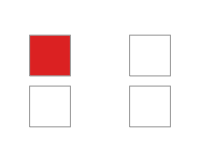
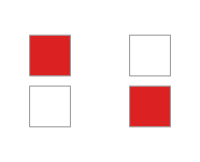
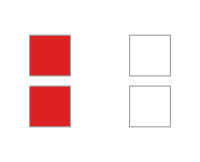
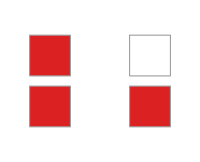
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules[1],ImageSize->200,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@Range[0,3,1]}]
```

As already mentioned, among these rules there are some that have the same behavior, which we can identify as a state permutation. That is, if we have 2 cellular automata whose states are {a,b} and {c,d}, and there exists a function that maps {a,b} -> {c,d} such that all relations in the transition function are preserved, we can say that these rules are identical.

For this case, if we perform the following rule mappings: {0, 1} -> {a,b} and {1,0} -> {b,a}, we find that rule  and  are equivalent. We can visualize this as if we simply swapped the colors:

```mathematica
Grid[{RulePlot[CellularAutomaton[{#,2,0}],ColorRules->colorRules[1],ImageSize->100,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@{0,3},
RulePlot[CellularAutomaton[{#,2,0}],ColorRules->{1->RGBColor[1., 1., 1.],0->RGBColor[0.857359, 0.131106, 0.132128]},ImageSize->100,PlotLegends->Placed[Subscript[#,2,1], Below]]&/@{0,3}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

State permutation is not unique to 2 states; in that case it is simple because it is just swapping one for the other. When we have more states, state permutation tells us to map all states through every possible permutation. This is the case for 3 states:

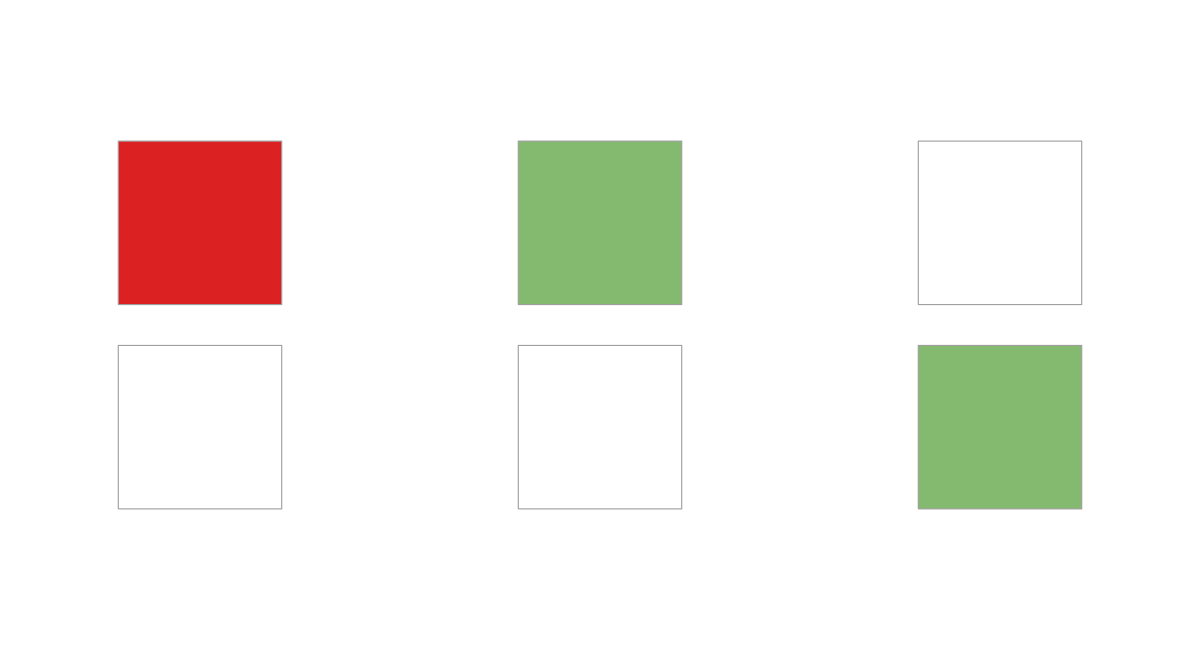
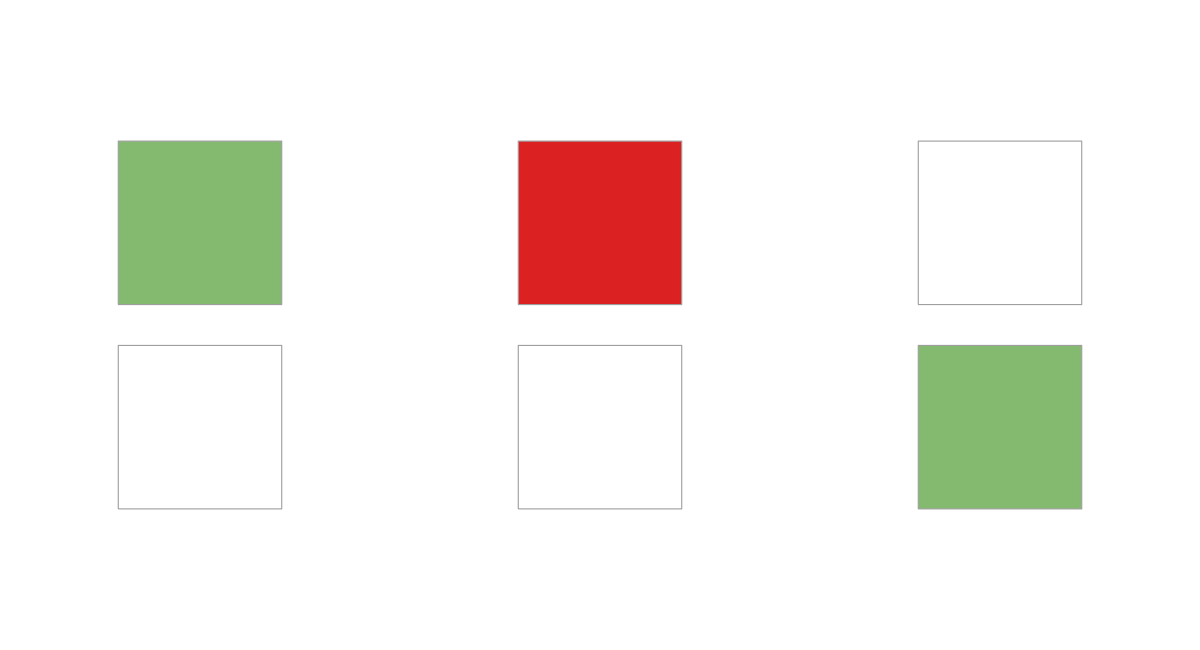
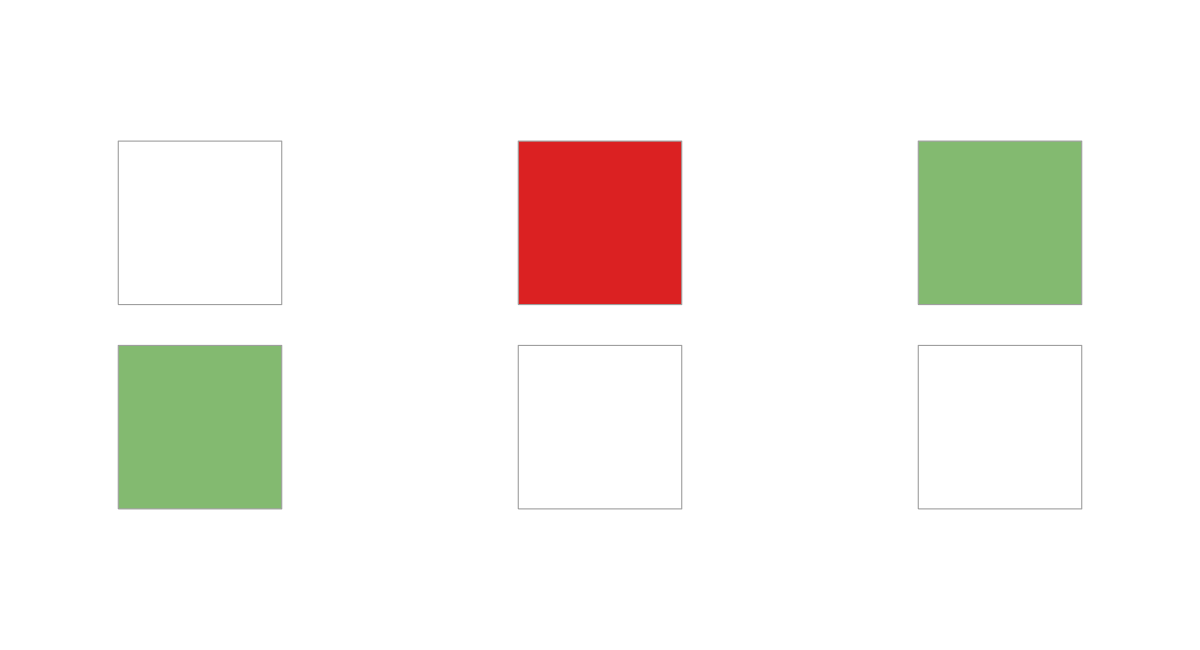
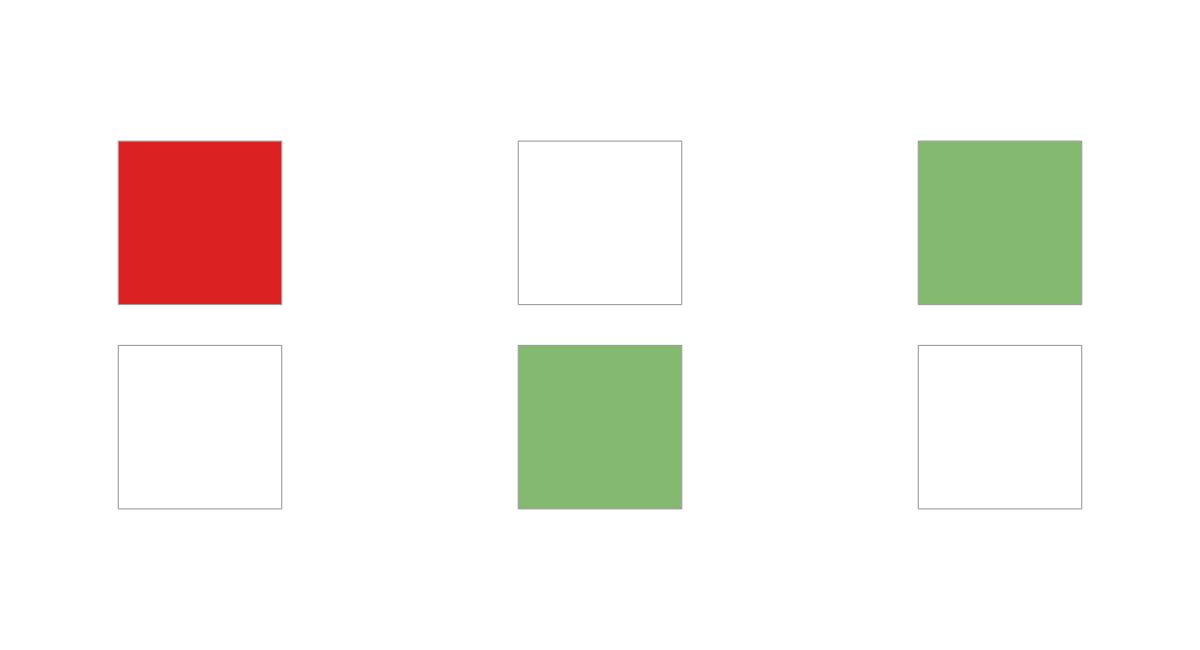
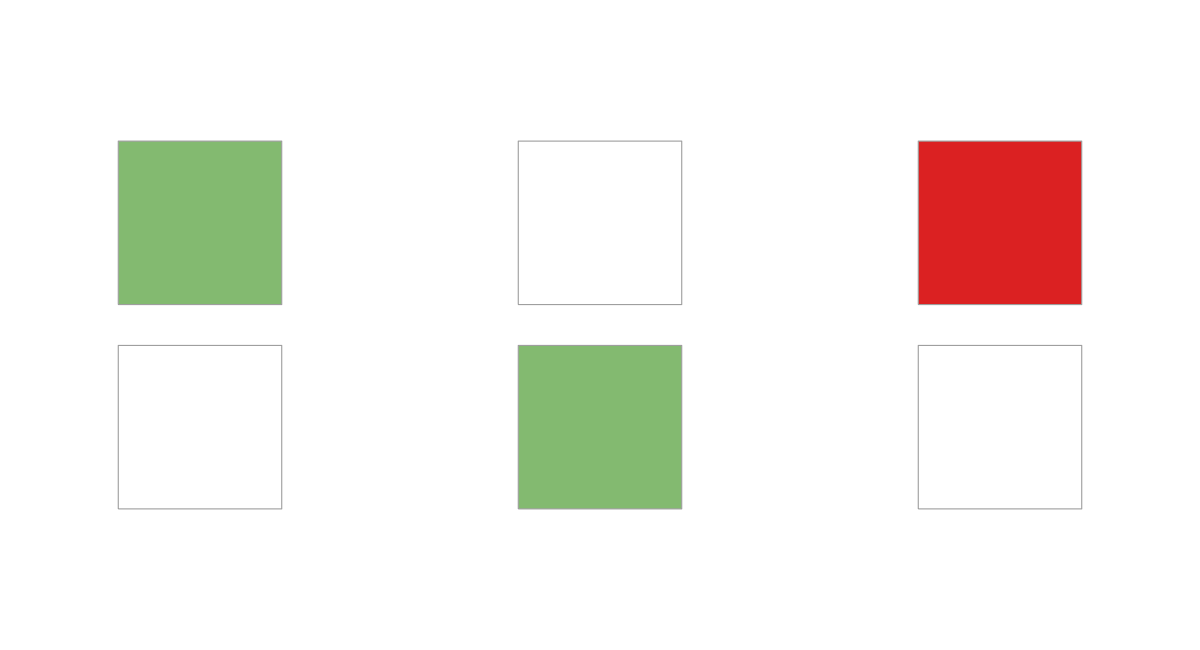
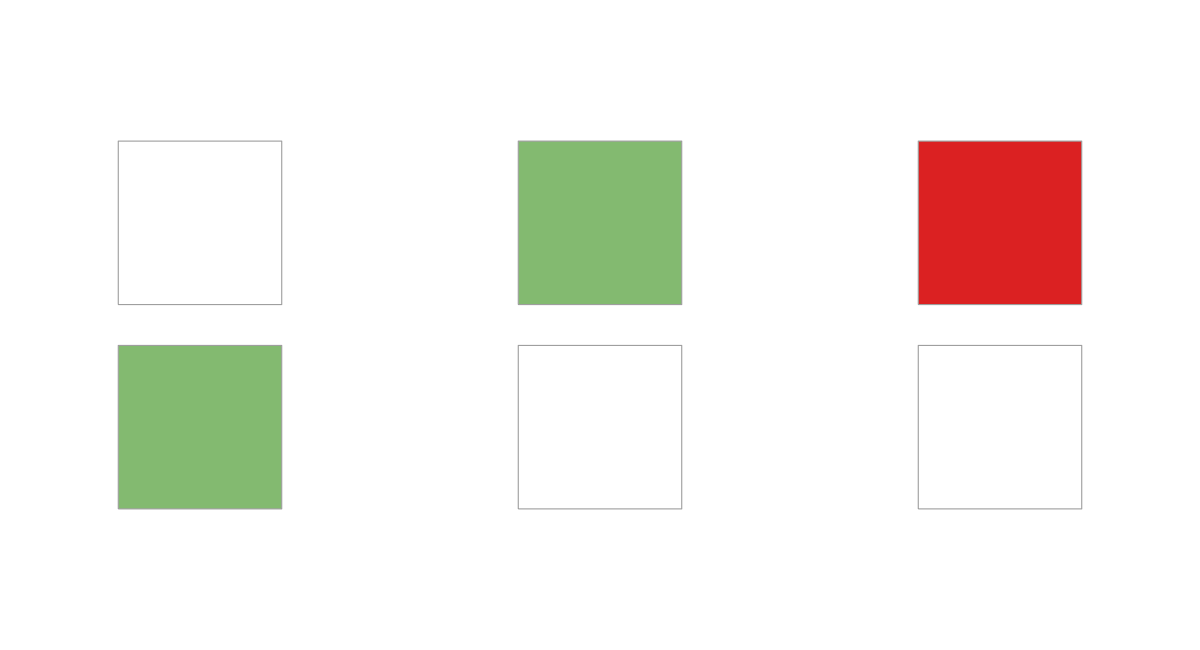
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
crs={{0->RGBColor[1., 1., 1.],1->RGBColor[0.513417, 0.72992, 0.440682],2->RGBColor[0.857359, 0.131106, 0.132128]},{0->RGBColor[1., 1., 1.],2->RGBColor[0.513417, 0.72992, 0.440682],1->RGBColor[0.857359, 0.131106, 0.132128]},{2->RGBColor[1., 1., 1.],0->RGBColor[0.513417, 0.72992, 0.440682],1->RGBColor[0.857359, 0.131106, 0.132128]},{1->RGBColor[1., 1., 1.],0->RGBColor[0.513417, 0.72992, 0.440682],2->RGBColor[0.857359, 0.131106, 0.132128]},{1->RGBColor[1., 1., 1.],2->RGBColor[0.513417, 0.72992, 0.440682],0->RGBColor[0.857359, 0.131106, 0.132128]},{2->RGBColor[1., 1., 1.],1->RGBColor[0.513417, 0.72992, 0.440682],0->RGBColor[0.857359, 0.131106, 0.132128]}};
Grid[Partition[Labeled[CaRulePlot[#[[1]],ColorRules->#[[2]]],#[[1]]]&/@Transpose[{InverseRules[],crs}],3]]
```

If we consider that all these rules have the same behavior, then the number of behaviors is smaller than the number of rules; we can see how the total number of behaviors drops drastically as the number of states increases.

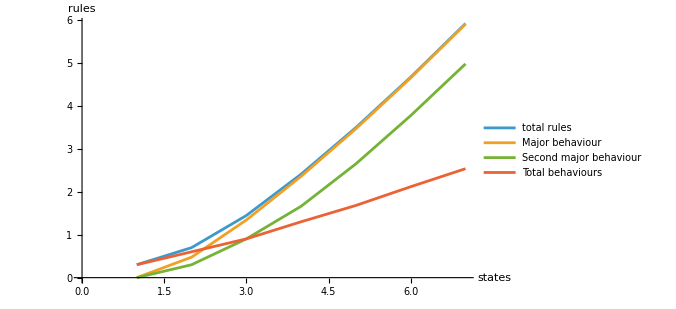

```mathematica
urs=;
ListLinePlot[
Transpose[MapThread[{#1^#1,#2[[-1,1]],If[Length[#2]>=2,#2[[-2,1]],0],Length[#2]}&,{Range[7],urs}]],
ScalingFunctions->"SignedLog",
PlotLegends->{"total rules","Major behaviour","Second major behaviour","Total behaviours"},
ImageSize->500,
AxesLabel->{"states", "rules"}
]
```

The following plot shows the rule vectors of the unique behaviors. We can observe that the rules with  states are a subset of the rules with  states where the new state has a transition to 0

```mathematica
burs=Table[IntegerDigits[#,Max[2,i],i]&/@urs[[i,;;,1]],{i,1,Length[urs]}];
Module[{cell=10,maxRows=50},
Grid[{With[{nrows=Min[maxRows,Dimensions[#][[1]]],
ncols=Dimensions[#][[2]]},
ArrayPlot[#[[;;UpTo[maxRows]]],
ColorRules->colorRules[5],
Mesh->True,
MeshStyle->Directive[GrayLevel[0.4],AbsoluteThickness[0.75]],
PlotRangePadding->0,
ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},
ImageSize->{cell*ncols,cell*maxRows}]]&/@burs
},Spacings->{2, 0}]
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

The next hypothesis was that there exists a mapping between rules that allows us to move between CA spaces. That is, we can move from rule  to  simply by adding a new state that points to state 0. Consider the following examples, where the pattern is shown to be exactly the same no matter how many states we add

Rules {0,0,0,0,0,0,0}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,0}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,0,0,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,0,0,1}&][[2;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,1,1,2}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,2}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,1,1,1}:

```mathematica
urv=Join[{<|"ca"->{0,1,0},"vector"->{0,0,0,0,0,0,0}|>},Table[
<|
"ca"->{#,i+1,0},
"vector"->IntegerDigits[#,Max[2,i+1],Length[urs]]
|>&/@urs[[i+1,;;,1]],
{i,1,Length[urs]-1}
]]//Flatten;
Module[{cas=CellularAutomaton[#,Range[#[[2]]-1,0,-1],3]&/@Select[urv,#["vector"]=={0,0,0,0,1,1,1}&][[;;,"ca"]],cell=15},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},Grid[{With[{nrows=Dimensions[#][[1]],ncols=Dimensions[#][[2]]},ArrayPlot[#,ColorRules->colorRules[6],Mesh->True,PlotRangePadding->0,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&/@cas}]]]
```

-Graphics- | -Graphics- | -Graphics-

We can carry out the reverse process and remove states. For this, 2 conditions must be satisfied:

The last state must transition to 0

No state may transition to the last state

However, when trying to apply this reduction we find that it fails for some rules, for example :

```mathematica
Grid[{Module[{cas={CellularAutomaton[{31,5,0},Range[4,0,-1],5],CellularAutomaton[{21,4,0},Range[3,0,-1],5],CellularAutomaton[{13,3,0},Range[2,0,-1],5]},labels={Subscript[31,5,1],Subscript[21,4,1],Subscript[13,3,1]},cell=30},With[{maxRows=Max[Dimensions[#][[1]]&/@cas]},MapThread[With[{nrows=Dimensions[#1][[1]],ncols=Dimensions[#1][[2]]},ArrayPlot[#1,ColorRules->colorRules[4],Mesh->True,PlotRangePadding->0,PlotLabel->#2,ImagePadding->{{0,0},{cell*(maxRows-nrows),0}},ImageSize->{cell*ncols,cell*maxRows}]]&,{cas,labels}]]]}]
```

-Graphics-

since neither rule  nor  belongs to the list of unique behaviors. But we can find the similarity through state permutation and navigate the connection graph, as shown below:

```mathematica
Module[{
vectors={{0,0,1,1,1},{0,1,1,1},{1,1,1},{0,0,0},{0,0},{0},{0,0,2,0},{0,2,0},{0,1,1},{1,1}},
edges={{0,0,1,1,1}->{0,1,1,1},{0,1,1,1}->{1,1,1},{1,1,1}->{0,0,0},{0,0,0}->{0,0},{0,0}->{0},{0,1,1,1}->{0,0,2,0},{0,0,2,0}->{0,2,0},{0,2,0}->{0,1,1},{0,1,1}->{1,1},{1,1}->{0,0}},
colores={({0,0,1,1,1}->{0,1,1,1})->Red,({1,1}->{0,0})->Blue,({0,1,1,1}->{1,1,1})->Red,({0,0,0}->{0,0})->Red,({0,0}->{0})->Red,({0,0,2,0}->{0,2,0})->Red,({0,1,1}->{1,1})->Red,({1,1,1}->{0,0,0})->Blue,({0,1,1,1}->{0,0,2,0})->Blue,({0,2,0}->{0,1,1})->Blue}},
Legended[LayeredGraph[
Graph[
edges,
EdgeStyle->colores,
VertexShapeFunction->(Inset[
ArrayPlot[{#2},
ColorRules->colorRules[2],
ImageSize->{Length[#2]*20,20},
Mesh->True,
MeshStyle->Gray,
ImagePadding->0,
PlotRangePadding->0
],#1]&),
VertexSize->{0.01,0.25}],
ImageSize->{450,Automatic}
],LineLegend[colores[[All,2]],{"Delete last state","Minor inverse rule"}]]
]
```

-Graphics-

With these 2 types of relations we can define the following connections, where each level represents the number of states, each label represents the representative rule of each unique behavior, and each arrow is a state reduction. It is no surprise that most of the connections point toward rule , keeping in mind that this is only for dimensionless CAs.

The next step is to increase the dimensionality and, therefore, the number of neighbors, starting with two neighbors and 2 states. We can again apply the state-permutation reduction, giving us the following rules

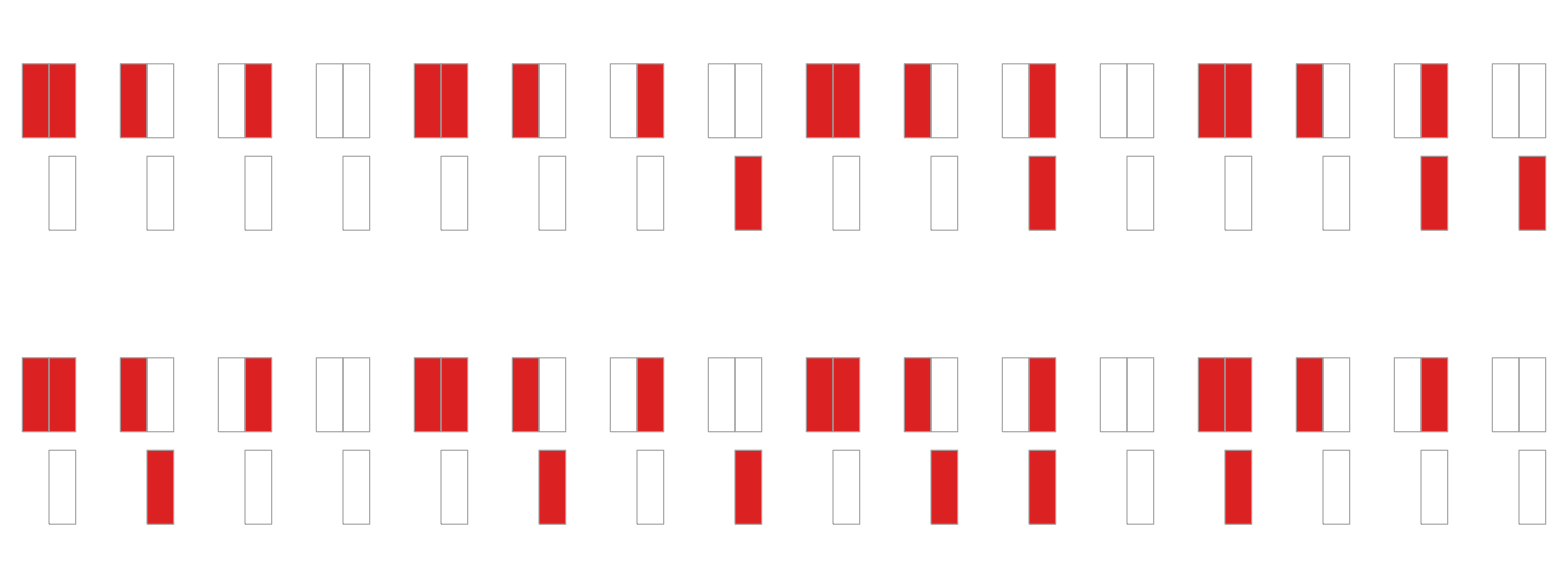

```mathematica
assoc=#[[1]]->#&/@DeleteDuplicates[InverseRules[Subscript@@{#,2,2}]&/@Range[0,15]];
Grid[Partition[CaRulePlot[Subscript@@#[[1]]]&/@assoc,4]]
```

Now we find another behavioral similarity: rules for which, if we reverse the evolution, we obtain the same behavior. This is the case for the following 2 rules:

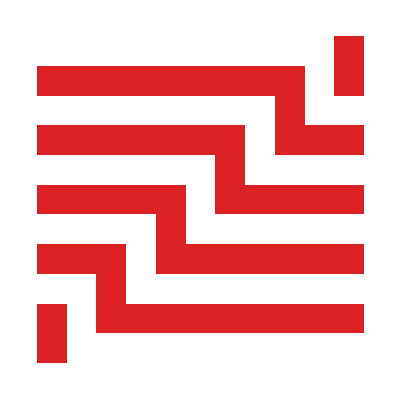
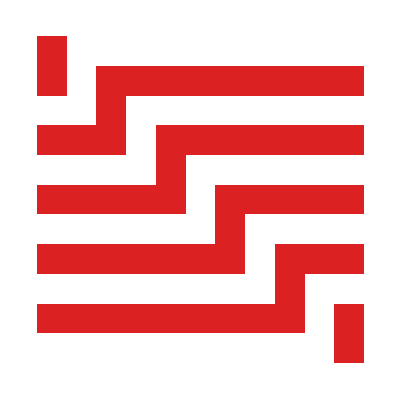
-Graphics- | -Graphics-

```mathematica
init={{1},0};
Grid[{{
RulePlot[CellularAutomaton[{3,2,ReverseSort[{{0},{1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules[1]],
RulePlot[CellularAutomaton[{5,2,ReverseSort[{{0},{-1}}]}],init,10,PlotLegends->"Text",ColorRules->colorRules[1]]}
}]
```

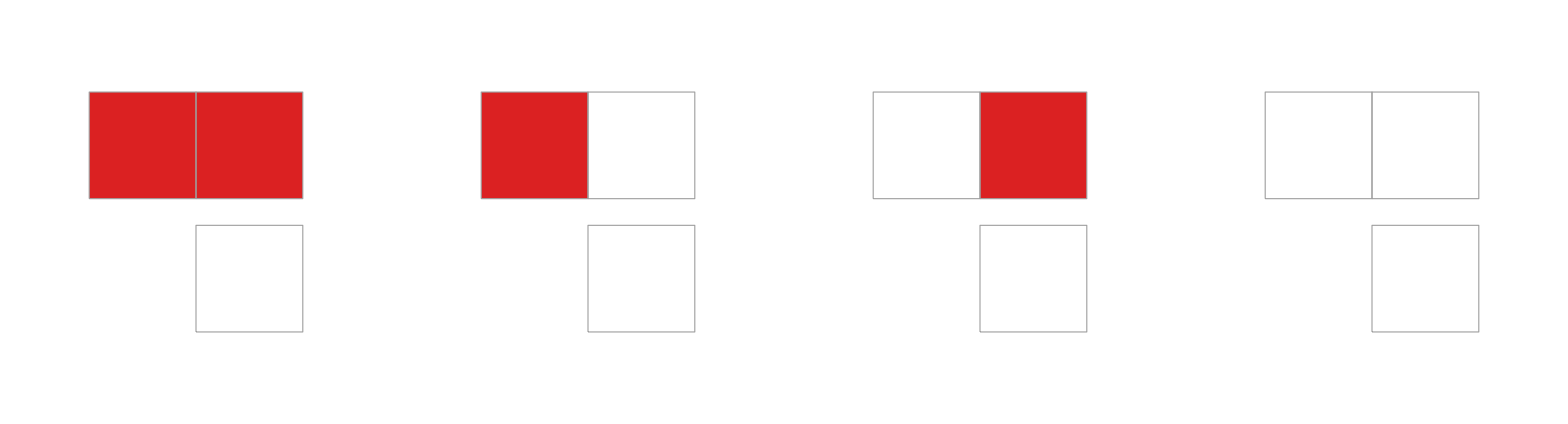
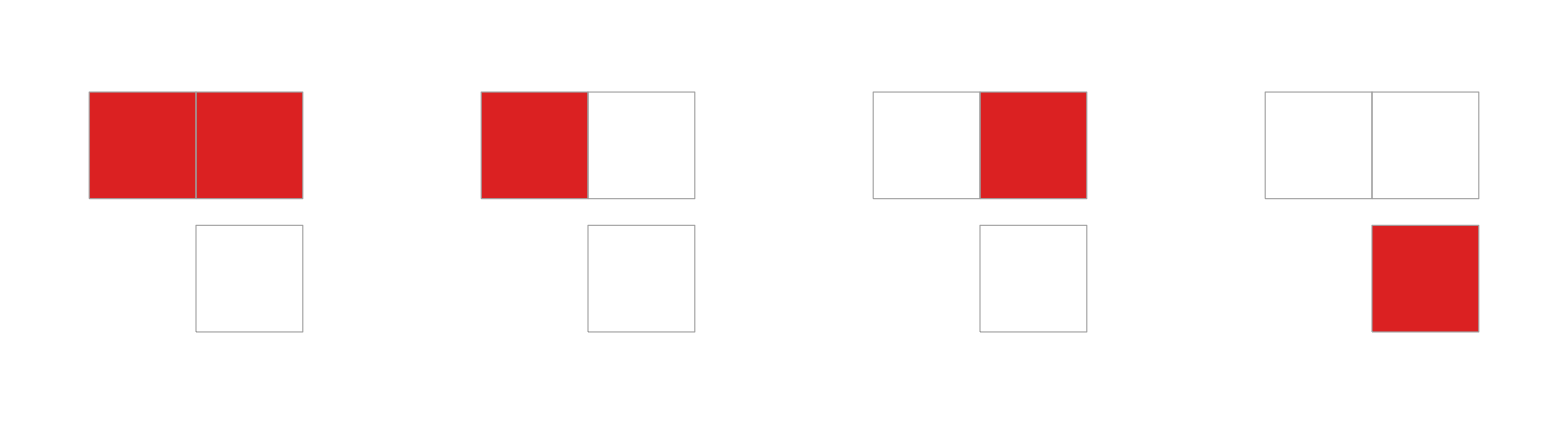
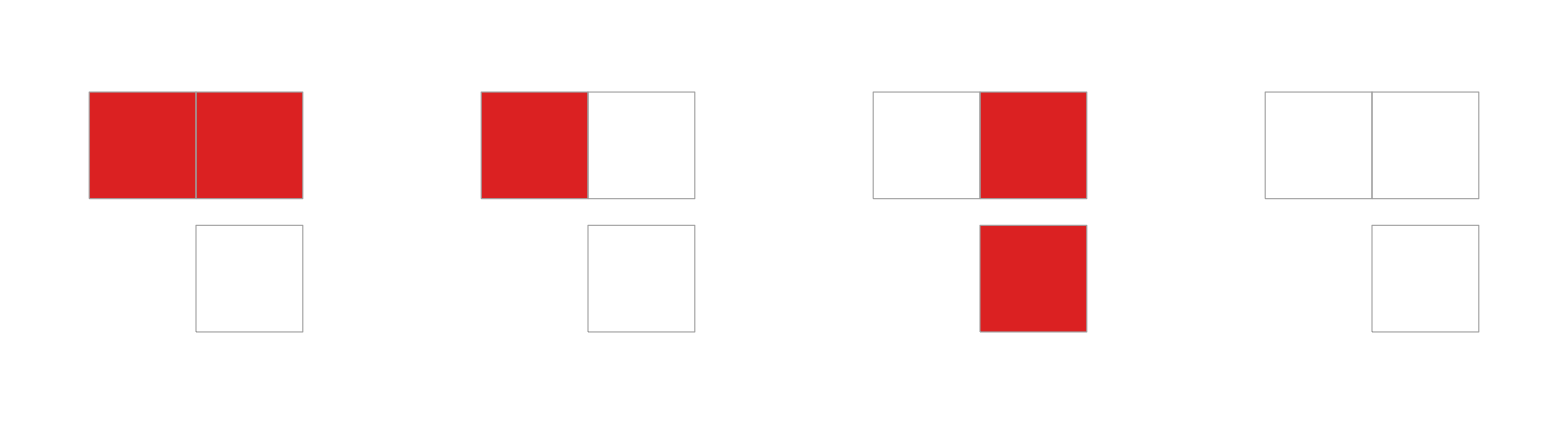
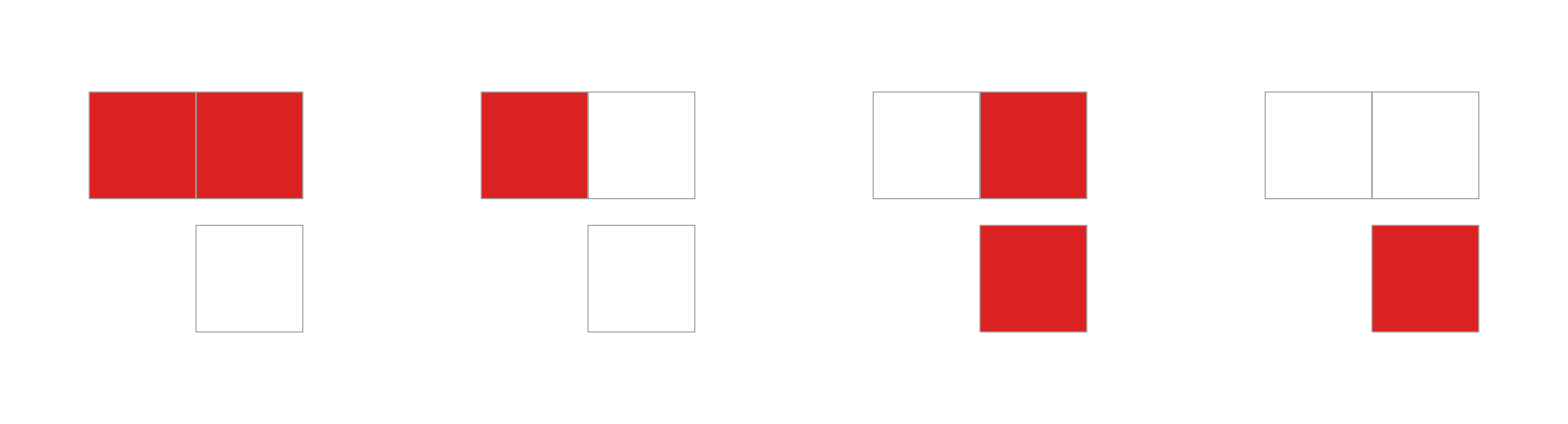
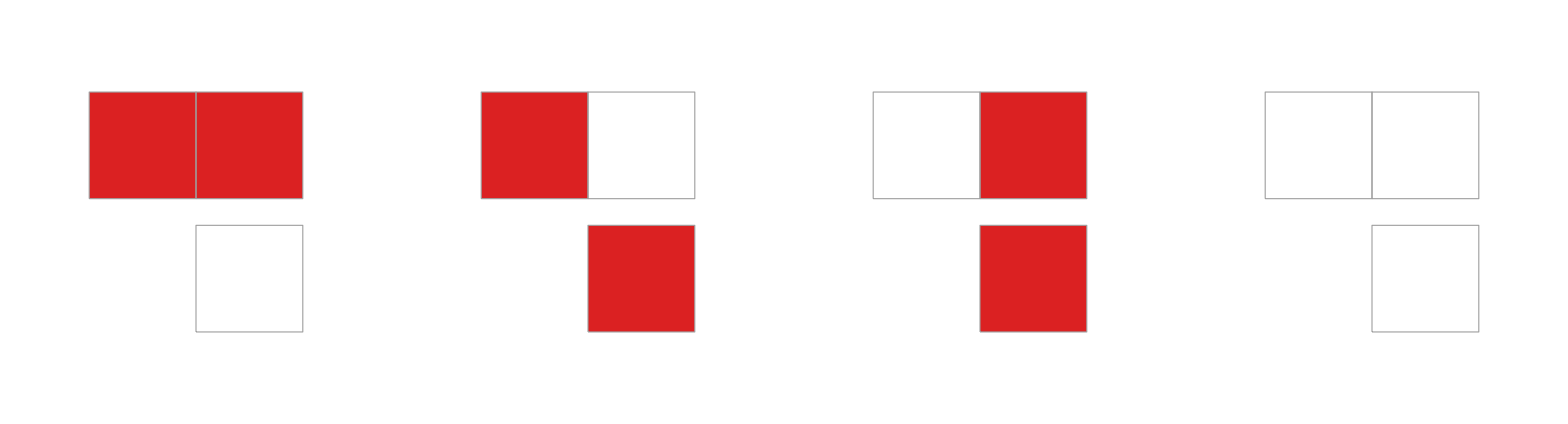
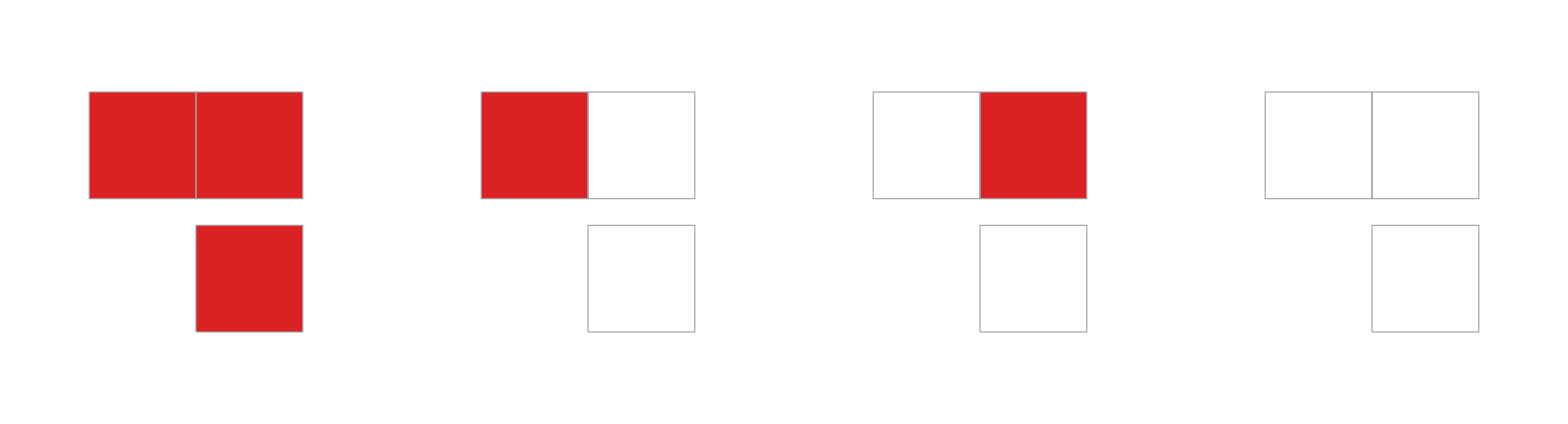
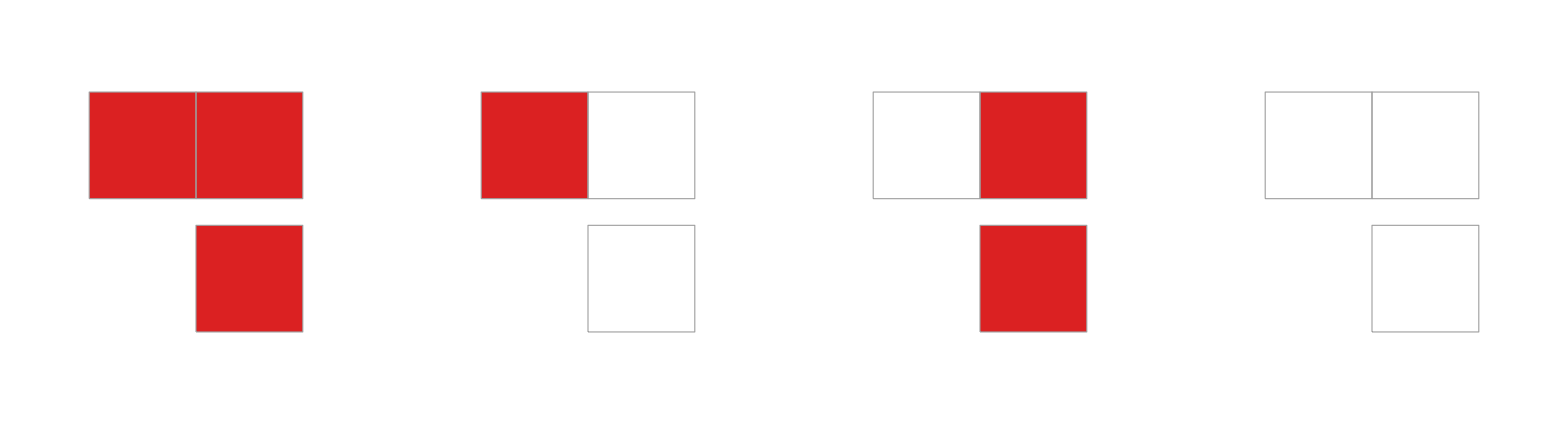
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Grid[Partition[CaRulePlot[Subscript@@{#,2,2}]&/@{0,1,2,3,6,8,10},UpTo[4]]]
```

From these behaviors, we find 3 relations with previous configurations.

Rule  does not depend on either one, just like  and

Rule  depends only on the left neighbor, so it mimics rule

Rule  depends only on the right neighbor, so it mimics rule

```mathematica
Grid[{{rulialGraph[{{0,2,1/2}->{0,1,1/2},{0,1,1/2}->{0,1,0},{0,2,1/2}->{0,2,0},{0,2,0}->{0,1,0}},Red],
rulialGraph[{{3,2,1/2}->{1,2,0}},Red],
rulialGraph[{{10,2,1/2}->{2,2,0}},Red]}}]
```

-Graphics-

The evolutions of rules  and  are exactly the same. For rule  and  we need to consider that it is the inverse of the cell to the left, so if we shift the blocks to the left, we find the same behavior.

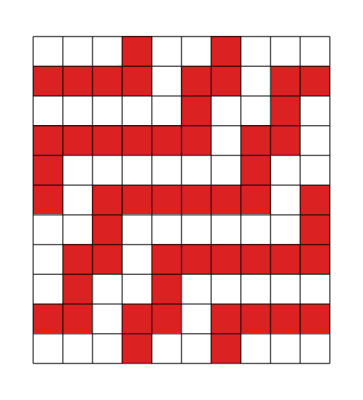
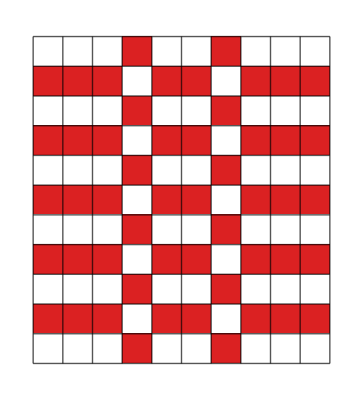
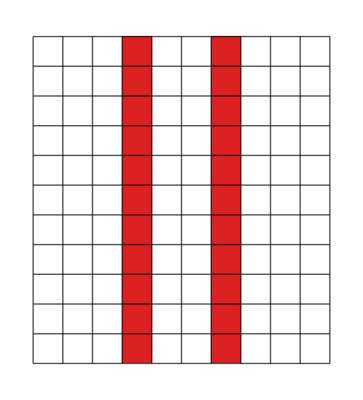
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
init={0,0,0,1,0,0,1,0,0,0};
Grid[{RulePlot[CellularAutomaton[#],init,10,PlotLegends->"Icon",ColorRules->colorRules[1],Mesh->True]&/@{{3,2,1/2},{1,2,0},{10,2,1/2},{2,2,0}}
}]
```

In the end, we have only 4 unique behaviors:

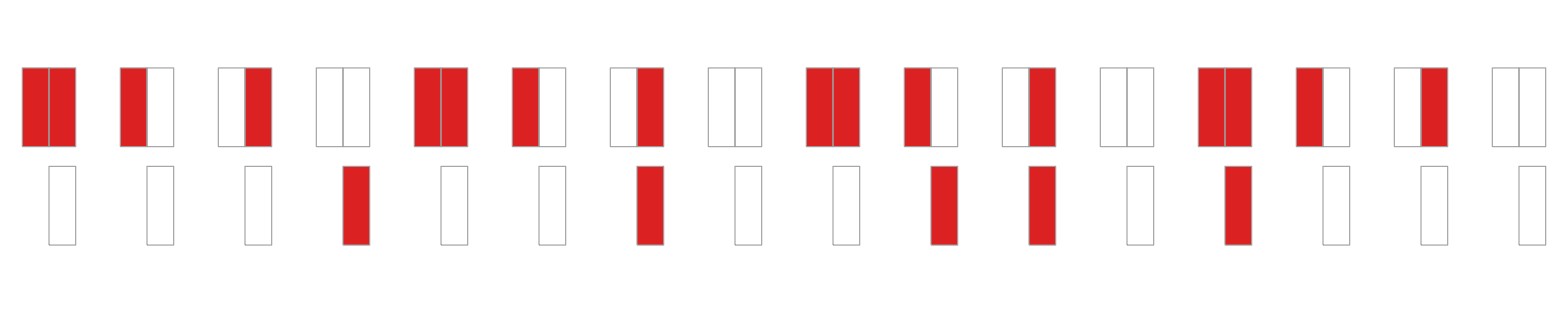

```mathematica
Grid[{CaRulePlot[Subscript@@{#,2,2}]&/@{1,2,6,8}}]
```

With random seeds, we find the following behaviors; none of them are reversible.

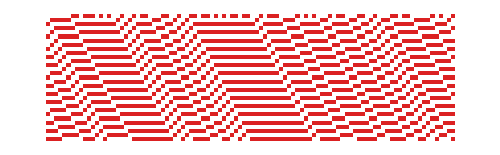
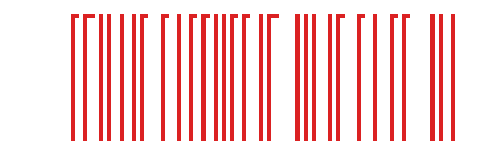
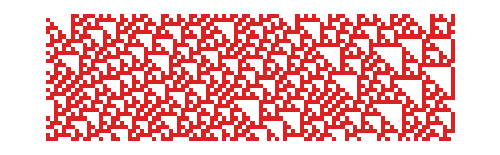
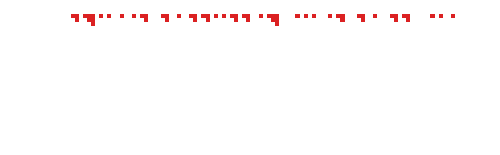
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
init=RandomInteger[{0,1},100];
Grid[Partition[RulePlot[CellularAutomaton[{#,2,1/2}],init,30,ColorRules->colorRules[1],ImageSize->500,PlotLegends->"Icon"]&/@{1,2,6,8},2]]
```

The similarity functions tell us that 2 rules have the same behavior within the same space. Inheritance rules mean that they are rules whose behavior can be obtained from a rule with either fewer states or fewer neighbors. The last step of this research is dimensionality reduction. It is the most complex step because, up to now, the neighbors have always been grouped together. If we say we have 2 neighbors, we assume those 2 neighbors are the 2 closest neighbors, because seeing this on a line is fairly simple; the problem is trying to see it now in 2 dimensions. By proximity, I can say that the 2 closest neighbors have 2 possibilities:

```mathematica
Grid[{{ArrayPlot[{{0,0,0},{1,2,1},{0,0,0}},ColorRules->colorRules[2],Mesh->True],ArrayPlot[{{0,1,0},{1,2,0},{0,0,0}},ColorRules->colorRules[2],Mesh->True]}}]
```

-Graphics-

And both have completely different behaviors, because even though the number of rules and the rule vector are equivalent: , one of them has a dimensionality reduction because it only considers the elements along one axis — in this case, the first one only considers left and right, regardless of the remaining dimensions. 
Another event that can happen is a neighborhood reduction that is later followed by a dimensionality reduction. 
Additionally, it will be necessary to start specifying the positions of the elements, because, for example, up to now we have assumed that the neighbors are always the closest ones to the center, even if there are only 2 of them, but we have not verified whether this holds for any 2 neighbors we might pick. This is because there are some configurations where it does hold true, but others where it needs to be investigated in depth.

For example, are the following 5 rules the same? We are assuming they are, but the only difference is which neighbors we are taking. So, under the definition we have been using, they are all rule , but their neighbors are in different positions; if we look closely, they seem to have the same behavior, only shifted or remapped, but the behavior appears to be the same for all of them. The Sierpinski triangle belongs to a different rule space.

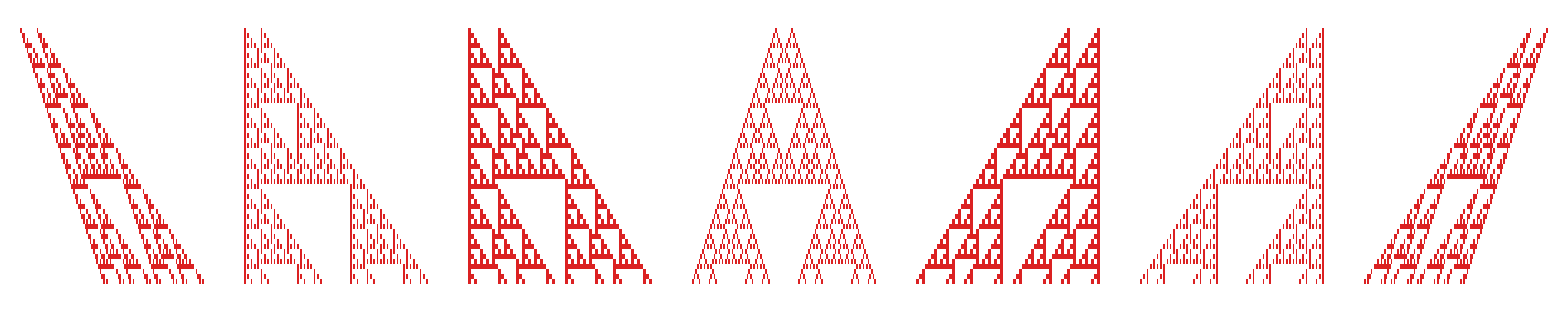

```mathematica
init={{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},0};
Grid[{{
ArrayPlot[CellularAutomaton[{6,2,{{-2},{-1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-2},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-1},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{-1},{1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{0},{1}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{2},{0}}},init,50],ColorRules->colorRules[1]],
ArrayPlot[CellularAutomaton[{6,2,{{2},{1}}},init,50],ColorRules->colorRules[1]]
}}]
```

With the following preloaded data, we show all the relations discovered for CAs with relatively small configurations:

```mathematica
data=addData[Join[getRules[2,1],getRules[3,1],getRules[2,2],getRules[3,2]]];
```

```mathematica
rdata=reduce[data];
```

However, all the experiments carried out so far only tell us whether 2 rules have the same behavior or not — a binary classification that does not tell us how similar these rules are based on their behaviors. Under this method, we would find that life-like rules are completely different from the Life rule, which is counterintuitive. The next step toward finding the similarity between rules is to compare the evolutions in the evolution graph.

## Evolution graph

For this part, what we will do is evolve a cellular automaton across all possible finite spaces. With this, we will build a transition graph that lets us compare the behavior of their transitions, looking for a similarity between these elements. Let's take as an example rule 0 and rule 255 of an ECA on a space of 5 cells:

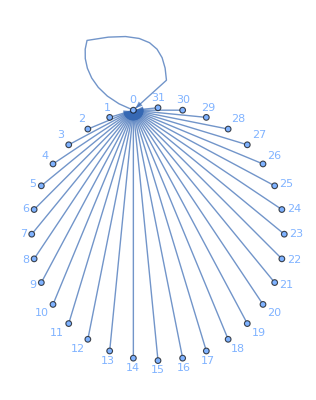
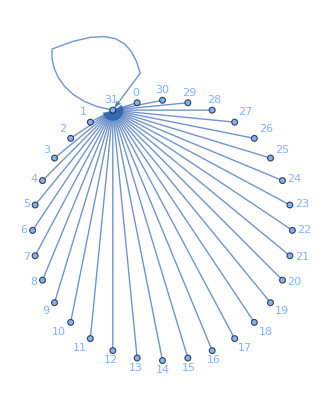
-Graphics-0_(2,3) | -Graphics-255_(2,3)

```mathematica
inits=Tuples[Range[0,1],5];
r255=FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&/@(CaArray[Subscript[255,2,3],#,1]&/@inits);
r0=FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&/@(CaArray[Subscript[0,2,3],#,1]&/@inits);
Grid[{{Labeled[Graph[r0,VertexLabels->Automatic,GraphLayout->"CircularEmbedding"],],Labeled[Graph[r255,VertexLabels->Automatic,GraphLayout->"CircularEmbedding"],]}},Frame->All]
```

Each node is a space represented in its decimal form. Each node has exactly one transition to another configuration. We see that rules  and  have exactly the same shape but differ in their labels. 
We can say that these 2 graphs are isomorphic, that is, there exists a bijective function that can map each vertex in the transition matrix — in this case, swapping 0 for 31

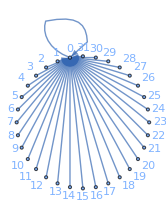
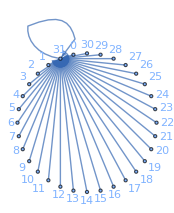
```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

If we only check whether two rules are isomorphic, we again get the same relations we already know, with the same binary classification. For this, 3 experiments were proposed with similar results:

## Canonical Form

We can also use the canonical form, an expression that shows a graph's topology without concerning ourselves with its labeling. This method only allows boolean comparisons, but it lets us identify and count the number of existing structures. To encode this, we use the following renaming algorithm:

We remove every leaf node and add it to a queue

For each leaf node we create a code relating it to its parent node, and remove the node

Si el nodo padre se convierte en un nodo hoja lo eliminamos y se añade a la cola

Once all leaf nodes are processed, the resulting cycles are encoded

That is, we prune down to the cycles, preserving every relation found along the way.

```mathematica
CanonFuncGraphQ[-Graphics-,-Graphics-]
```

True

We obtain the canonical form of the ECA rules at different sizes, to find the relations.

```mathematica
groups=ParallelTable[Module[{cfs},
cfs={#,CanonFuncGraph[MakeGraph[Subscript[#,2,3],i]]}&/@Range[0,255];
Values[GroupBy[cfs,#[[2]]&]][[;;,;;,1]]
]
,{i,1,12,1}];
```

```mathematica
ListLinePlot[Labeled[#,#]&/@Length/@groups,AxesLabel->{"space size", "behaviours"},InterpolationOrder->0.1,Filling->Bottom]
```

-Graphics-

The larger the space, the more distinctions we can make between rules, but this does not keep growing with the space — it has a limit. For ECA, with spaces of 4 cells we can already distinguish almost all of the real or already-classified behaviors. This raises another question: how do we define the right minimum size so as not to lose information?

Although this method lets us find the same classifications, it doesn't work as an index, because the similarity it gives is exact. To try to fix this, we will use the following method, which computes the Eigenvalues and uses them as a feature vector.

## Eigenvalues

A graph can be represented as a matrix, and from that matrix we can obtain the eigenvalues, a vector of values that tells us their level of importance within the matrix. For this, we apply the following process:

We extract the transition matrix

We compute the matrix's eigenvalues

We compare the 2 vectors with cosine distance.

```mathematica
ev0=Eigenvalues[N@Normal[AdjacencyMatrix[-Graphics-]]]
ev255=Eigenvalues[N@Normal[AdjacencyMatrix[-Graphics-]]]
```

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

If the distance is 0 it means the rules are equivalent. But since this is not a symmetric matrix, the eigenvalues can have an imaginary part. To handle this we can either double the dimensionality into real and complex parts, or build an intermediate measure that groups them, such as cosine distance.

```mathematica
Eigenvalues[N@Normal[AdjacencyMatrix[MakeGraph[,4]]]]
EigenvaluesGraph[MakeGraph[,4]]
```

{-2.25642×10^-18+1. ⅈ,-2.25642×10^-18-1. ⅈ,-0.707107+0.707107 ⅈ,-0.707107-0.707107 ⅈ,-1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,0.707107+0.707107 ⅈ,0.707107-0.707107 ⅈ,1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

{-2.25642×10^-18,1.,-2.25642×10^-18,-1.,-0.707107,0.707107,-0.707107,-0.707107,-1.,0.,1.,0.,-1.,0.,0.707107,0.707107,0.707107,-0.707107,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

We can apply cosine distance and get a similarity measure between different rules. The plot below shows the relation between the 256 ECA rules.

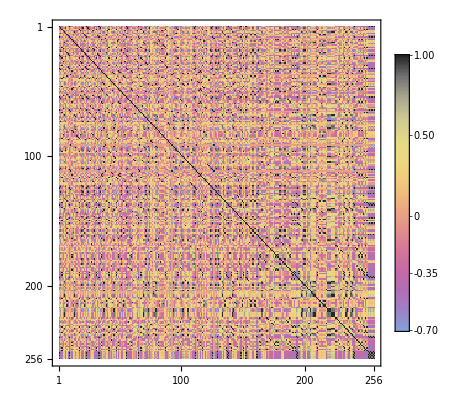

```mathematica
ecaGraphs=ParallelTable[MakeGraph[Subscript[i,2,3],5],{i,0,255,1}];
distances=1-DistanceMatrix[ecaGraphs,DistanceFunction->EigenvaluesGraphDistance];
MatrixPlot[distances,ColorFunction->"CMYKColors",PlotLegends->Automatic]
```

However, with this method, although we can find the relations between different rules, a problem arises: we cannot compare rules from different spaces, since the number of nodes is what defines the vector's length, and there would be no way to map the relations without losing information:

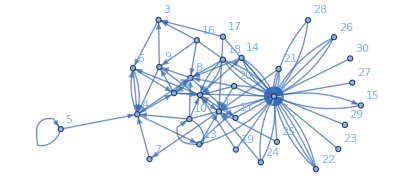
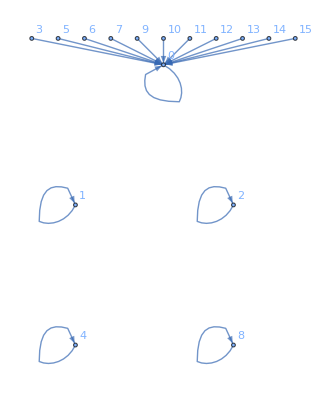
4_(3,2) | 4_(2,4)
-Graphics- | -Graphics-
Total vertex:31 | Total vertex:16
{2.67226,-1.66919,0.436134,0.436134,-1.05038,-1.05038,1.,-1.,1.,1.,-0.174314,-0.174314,-0.275455,-0.275455,0.706521,0.418448,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} | {1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Grid[Transpose[Module[{g},
Table[
g=MakeGraph[i,4];
{
i,
g,
"Total vertex:"<>ToString[Length[VertexList[g]]],
Re[Eigenvalues[N[Normal[AdjacencyMatrix[g]]]]]
},
{i,{,}}]
]],
Frame->All
]
```

This is why a new method is used, which instead of directly computing the eigenvalues, counts cycles at different periods

## Spectral Moments

Instead of comparing the full spectrum, we compare a fixed number of spectra.
We evolve rule  steps across every possible configuration and define the fraction  as the proportion of configurations that returned to their initial configuration after   steps.

For example, taking rule 30 with 5 spaces, if we evolve it one step () only 3 nodes map to themselves (); the same happens when we evolve 2, 3, 4 steps, etc. But when we evolve it 8 times, we see that 11 configurations returned to their initial configuration ().

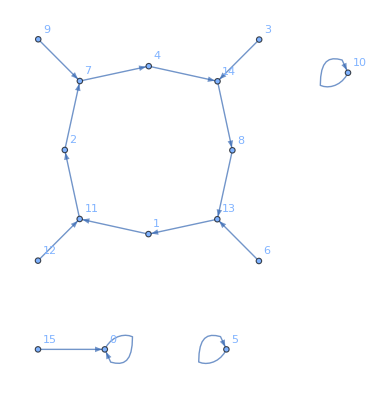
```mathematica
Grid[{{,-Graphics-,<|""->3,""->3,""->3,""->3,""->3,""->3,""->3,""->11|>}},Frame->All]
```

With this method, we can again build the similarity matrix between all these rules, but additionally we can compare all of them, even rules from different spaces.

```mathematica
ecaGraphs=ParallelTable[MakeGraph[Subscript[i,2,3],12],{i,0,255,1}];
momentsVectors=ParallelTable[SpectralMoments[g,14],{g,ecaGraphs}];
```

{44,60,71,71,71,71,72,72,72,72,73,73,73,73,73}

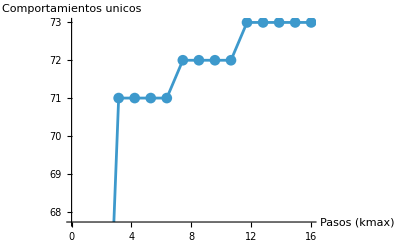

```mathematica
uniqueCounts=Table[momVecs=ParallelTable[SpectralMoments[g,kmax],{g,ecaGraphs}];Length[DeleteDuplicates[momVecs]],{kmax,2,16}]
ListLinePlot[uniqueCounts,DataRange->{1,16},PlotMarkers->Automatic,AxesLabel->{"Pasos (kmax)","Comportamientos unicos"}]
```

To identify at which combination of steps and space size real results start to appear, we repeat the previous test also varying the space size, building a results matrix. Red points mark combinations with more than 60 unique behaviors.

```mathematica
spaceSizes=Range[1,12];stepsRange=Range[2,16];resultsMatrix=Table[ecaGraphsS=ParallelTable[MakeGraph[Subscript[i, 2,3],s],{i,0,255,1}];Table[momVecs=ParallelTable[SpectralMoments[g,kmax],{g,ecaGraphsS}];Length[DeleteDuplicates[momVecs]],{kmax,stepsRange}],{s,spaceSizes}]
```

{{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8},{12,21,21,21,24,24,24,24,24,24,24,24,24,24,24},{29,29,47,47,47,47,52,52,52,52,52,52,52,52,52},{20,22,22,35,36,36,36,36,44,44,44,44,44,49,49},{36,55,56,56,64,64,64,65,65,65,68,68,68,68,68},{25,26,27,28,28,43,43,43,43,43,43,43,56,56,56},{39,40,58,58,59,59,67,67,67,67,67,67,67,67,69},{30,45,46,46,49,50,50,64,64,64,64,64,64,64,64},{35,38,40,62,63,63,63,63,68,68,68,68,68,71,71},{28,29,30,32,32,33,33,33,33,51,51,51,51,51,51},{44,60,71,71,71,71,72,72,72,72,73,73,73,73,73}}

```mathematica
spaceSizes=Range[1,12];stepsRange=Range[2,16];resultsMatrix=Table[ecaGraphsS=ParallelTable[MakeGraph[Subscript[i, 2,3],s],{i,0,255,1}];Table[momVecs=ParallelTable[SpectralMoments[g,kmax],{g,ecaGraphsS}];Length[DeleteDuplicates[momVecs]],{kmax,stepsRange}],{s,spaceSizes}]
```

{{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8},{12,21,21,21,24,24,24,24,24,24,24,24,24,24,24},{29,29,47,47,47,47,52,52,52,52,52,52,52,52,52},{20,22,22,35,36,36,36,36,44,44,44,44,44,49,49},{36,55,56,56,64,64,64,65,65,65,68,68,68,68,68},{25,26,27,28,28,43,43,43,43,43,43,43,56,56,56},{39,40,58,58,59,59,67,67,67,67,67,67,67,67,69},{30,45,46,46,49,50,50,64,64,64,64,64,64,64,64},{35,38,40,62,63,63,63,63,68,68,68,68,68,71,71},{28,29,30,32,32,33,33,33,33,51,51,51,51,51,51},{44,60,71,71,71,71,72,72,72,72,73,73,73,73,73}}

-Graphics3D-

```mathematica
ListPlot3D[resultsMatrix,DataRange->{{2,16},{1,8}},AxesLabel->{"Pasos","Tamano del espacio","Comportamientos unicos"},ColorFunction->(If[#3>60,Red,Blue]&),ColorFunctionScaling->False,Mesh->All]
```

-Graphics3D-

We test an alternative construction of the functional graph: instead of every configuration of the space being a distinct node, we identify all configurations that are cyclic rotations of each other (for example, in a 4-cell space, 0001, 0010, 0100 and 1000 are stored as the same node). This is well defined because CaArray uses a cyclic boundary and the rule is homogeneous: rotating the initial state and evolving gives the same result, rotated, as evolving and then rotating.

```mathematica
RotClass[state_List]:=First[Sort[NestList[RotateLeft,state,Length[state]-1]]]
```

```mathematica
MakeGraphRot[ca_Subscript,spaceSize_]:=Module[{classes},classes=DeleteDuplicates[RotClass/@Tuples[Range[0,ca⟦2⟧-1],spaceSize]];Graph[(FromDigits[RotClass[#1⟦1⟧],2]->FromDigits[RotClass[#1⟦2⟧],2]&)/@(CaArray[ca,#1,1]&)/@classes,VertexLabels->Automatic]]
```

The number of nodes no longer depends on the rule, only on the space size (it is the number of distinct binary necklaces under rotation):

```mathematica
testRules={15,85,170,240,30};sizesRange=Range[2,8];
```

```mathematica
nodeGrid=Grid[Prepend[Transpose[{sizesRange,2^sizesRange,Table[VertexCount[MakeGraphRot[Subscript[15, 2,3],s]],{s,sizesRange}]}],{"Tamano del espacio","Nodos (MakeGraph)","Nodos (MakeGraphRot)"}],Frame->All,Alignment->Left]
```

Tamano del espacio | Nodos (MakeGraph) | Nodos (MakeGraphRot)
2 | 4 | 3
3 | 8 | 4
4 | 16 | 6
5 | 32 | 8
6 | 64 | 14
7 | 128 | 20
8 | 256 | 36

We now compare this construction against MakeGraph using rules 15, 85, 170 and 240 (already known to merge under CanonFuncGraph) plus rule 30 as a reference, checking at which space sizes each pair merges:

```mathematica
pairwiseMerges[graphBuilder_]:=Table[gs=(graphBuilder[Subscript[#1, 2,3],s]&)/@testRules;pairs=Subsets[Range[5],{2}];Select[pairs,CanonFuncGraphQ[gs⟦#1⟦1⟧⟧,gs⟦#1⟦2⟧⟧]&],{s,sizesRange}]
```

```mathematica
mergesOrig=pairwiseMerges[MakeGraph];mergesRot=pairwiseMerges[MakeGraphRot];idxToRules[pairs_]:=If[pairs==={},"ninguna",StringRiffle[(ToString[testRules⟦#1⟦1⟧⟧]<>"~"<>ToString[testRules⟦#1⟦2⟧⟧]&)/@pairs,", "]];summaryGrid=Grid[Prepend[Transpose[{sizesRange,idxToRules/@mergesOrig,idxToRules/@mergesRot}],{"Tamano","Fusiones (MakeGraph)","Fusiones (MakeGraphRot)"}],Frame->All,Alignment->Left]
```

Tamano | Fusiones (MakeGraph) | Fusiones (MakeGraphRot)
2 | 15~85, 15~170, 15~240, 85~170, 85~240, 170~240 | 15~85, 170~240
3 | 15~85, 170~240 | 15~85, 170~240
4 | 15~85, 15~170, 15~240, 85~170, 85~240, 170~240 | 15~85, 170~240
5 | 15~85, 170~240 | 15~85, 170~240
6 | 15~85, 15~170, 15~240, 85~170, 85~240, 170~240 | 15~85, 170~240
7 | 15~85, 170~240 | 15~85, 170~240
8 | 15~85, 15~170, 15~240, 85~170, 85~240, 170~240 | 15~85, 170~240

With MakeGraph, the 4 rules merge completely only at even sizes (2, 4, 6, 8); at odd sizes only the pairs 15~85 and 170~240 merge. With MakeGraphRot that even/odd pattern disappears: at every size tested, only 15~85 and 170~240 merge, never all 4 together. This suggests that the full 4-rule merge at even sizes is an artifact of that parity in the original construction, and not a real property of the rules.

```mathematica
spaceSizesRot=Range[1,16];resultsMatrixRot=Table[ecaGraphsRotS=ParallelTable[MakeGraphRot[Subscript[i, 2,3],s],{i,0,255,1}];Table[momVecs=ParallelTable[SpectralMoments[g,kmax],{g,ecaGraphsRotS}];Length[DeleteDuplicates[momVecs]],{kmax,stepsRange}],{s,spaceSizesRot}]
```

{{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8},{14,14,14,14,14,14,14,14,14,14,14,14,14,14,14},{17,23,25,25,26,26,26,26,26,26,26,26,26,26,26},{25,28,29,30,30,30,30,30,30,30,30,30,30,30,30},{27,30,33,34,34,37,37,38,38,38,38,38,39,39,39},{37,44,47,48,48,48,48,48,48,48,48,48,48,49,49},{35,39,41,41,42,45,47,47,47,47,47,47,47,47,47},{47,59,59,60,60,60,60,60,60,60,60,60,60,60,60},{44,45,48,49,49,50,50,50,50,50,50,50,51,51,52},{50,56,56,58,58,58,58,58,58,58,58,58,58,58,58},{49,51,52,53,53,54,54,54,54,54,54,54,54,54,54},{58,58,62,62,62,63,63,63,63,63,63,63,63,63,63},{50,52,55,55,55,55,55,55,55,55,55,55,55,55,55},{55,56,56,56,56,56,56,56,56,56,56,56,56,57,57}}

```mathematica
comparisonGrid=GraphicsGrid[{{ListPlot3D[resultsMatrix,DataRange->{{2,16},{1,8}},AxesLabel->{"Pasos","Tamano del espacio","Comportamientos unicos"},ColorFunction->(If[#3>60,Red,Blue]&),ColorFunctionScaling->False,Mesh->All,PlotLabel->"MakeGraph"],ListPlot3D[resultsMatrixRot,DataRange->{{2,16},{1,16}},AxesLabel->{"Pasos","Tamano del espacio","Comportamientos unicos"},ColorFunction->(If[#3>60,Red,Blue]&),ColorFunctionScaling->False,Mesh->All,PlotLabel->"MakeGraphRot"]}},ImageSize->900]
```

-Graphics-

With MakeGraphRot the maximum number of unique behaviors observed is 49, so no combination of steps and space size exceeds the threshold of 60 (the grid stays entirely blue). This is consistent with MakeGraphRot producing smaller graphs (fewer nodes, from identifying rotations), which reduces the number of distinct possible spectral-moment vectors.

## Game of Life

In this chapter we apply the same methods (functional graph quotiented by symmetries, and spectral moments) to Conway's Game of Life and two life-like variants, to see whether the comparison generalizes to a 2-dimensional cellular automaton.

We define the evolution step on a toroidal grid (cyclic boundary on both axes, the same philosophy as CaArray in 1D), with Moore neighborhood (8 neighbors) and birth/survival rules given by sets of live-neighbor counts.

```mathematica
rows=4;cols=4;
```

```mathematica
neighborSum2D[state_?MatrixQ]:=Total[(RotateLeft[state,#1]&)/@{{-1,-1},{-1,0},{-1,1},{0,-1},{0,1},{1,-1},{1,0},{1,1}}];Life2DStep[state_?MatrixQ,birthSet_List,survivalSet_List]:=Module[{nb},nb=neighborSum2D[state];MapThread[If[#1==1,If[MemberQ[survivalSet,#2],1,0],If[MemberQ[birthSet,#2],1,0]]&,{state,nb},2]]
```

We check the implementation against known Game of Life patterns: a block (still life) should stay unchanged, and a horizontal blinker should rotate to vertical.

```mathematica
block={{1,1,0,0},{1,1,0,0},{0,0,0,0},{0,0,0,0}};blinker={{0,0,0,0},{1,1,1,0},{0,0,0,0},{0,0,0,0}};{Life2DStep[block,{3},{2,3}]==block,Life2DStep[blinker,{3},{2,3}]}
```

{True,{{0,1,0,0},{0,1,0,0},{0,1,0,0},{0,0,0,0}}}

The graph-construction method combining permutations that we used in 1D identified cyclic rotations. Its natural analog in 2D is identifying configurations that are toroidal translations of each other (shifts in x and y, with wraparound):

```mathematica
TransClass2D[flat_List]:=First[Sort[Flatten/@Flatten[Table[RotateLeft[RotateLeft[Partition[flat,cols],i],{0,j}],{i,0,rows-1},{j,0,cols-1}],1]]]
```

We propose a 4x4 toroidal grid (16 cells): this gives 2^16 = 65536 raw configurations, the same scale already tested in 1D at size=16 (computationally feasible, ~0.3s per rule there), and large enough for non-trivial Life patterns (oscillators, etc.) to appear.

```mathematica
classes2D=DeleteDuplicates[ParallelMap[TransClass2D,Tuples[{0,1},rows cols]]]
```

4156

```mathematica
MakeGraphLife2D[birthSet_List,survivalSet_List,classes_List]:=Module[{succ},succ[flat_List]:=TransClass2D[Flatten[Life2DStep[Partition[flat,cols],birthSet,survivalSet]]];Graph[(FromDigits[#1,2]->FromDigits[succ[#1],2]&)/@classes,VertexLabels->Automatic]]
```

The 3 rules to compare (B/S notation = birth/survival by live-neighbor count): standard Life (B3/S23), Life where a cell also stays alive if all 8 neighbors are alive (B3/S238), and Life where a cell also revives if all 8 neighbors are alive (B38/S23).

```mathematica
gLife=MakeGraphLife2D[{3},{2,3},classes2D];gLifeS8=MakeGraphLife2D[{3},{2,3,8},classes2D];gLifeB8=MakeGraphLife2D[{3,8},{2,3},classes2D];
```

Instead of guessing the number of steps needed, we first build the 3 graphs and measure the actual cycle lengths that appear in them, setting kmax to the maximum found among the 3 rules -- so the spectral-moments vector captures all the real periodicity without wasting computation.

```mathematica
GraphCycleLengths[g_Graph]:=Module[{verts,index,f,n,succ,indeg,resto,queue,qi,v,visited,cycles},verts=VertexList[g];n=Length[verts];index=AssociationThread[verts,Range[n]];succ=Association[(#1⟦1⟧->#1⟦2⟧&)/@EdgeList[g]];f=Table[index[succ[v]],{v,verts}];indeg=ConstantArray[0,n];Do[indeg⟦f⟦i⟧⟧++,{i,n}];resto=indeg;queue=Flatten[Position[resto,0]];qi=1;While[qi≤Length[queue],v=queue⟦qi++⟧;If[--resto⟦f⟦v⟧⟧==0,AppendTo[queue,f⟦v⟧]]];visited=ConstantArray[False,n];cycles={};Do[If[resto⟦v⟧>0&&!visited⟦v⟧,Module[{c={},w=v},While[!visited⟦w⟧,visited⟦w⟧=True;AppendTo[c,w];w=f⟦w⟧];AppendTo[cycles,Length[c]]]],{v,n}];cycles]
```

```mathematica
cyclesLife=GraphCycleLengths[gLife];cyclesLifeS8=GraphCycleLengths[gLifeS8];cyclesLifeB8=GraphCycleLengths[gLifeB8];kmaxLife=Max[Join[cyclesLife,cyclesLifeS8,cyclesLifeB8]]
```

8

We compute and preserve the 3 spectral-moments vectors (kmax=8) explicitly, in a table alongside each rule's name:

```mathematica
vecLife=SpectralMoments[gLife,kmaxLife];vecLifeS8=SpectralMoments[gLifeS8,kmaxLife];vecLifeB8=SpectralMoments[gLifeB8,kmaxLife];ruleNames={"Life (B3/S23)","Life+S8 (B3/S238)","Life+B8 (B38/S23)"};vectorTable=Grid[Prepend[Transpose[{ruleNames,{vecLife,vecLifeS8,vecLifeB8}}],{"Rule","Spectral moments vector"}],Frame->All,Alignment->Left]
```

Rule | Spectral moments vector
Life (B3/S23) | {0.00433109,0.00914341,0.00433109,0.00914341,0.00433109,0.00914341,0.00433109,0.020693}
Life+S8 (B3/S238) | {0.0045717,0.0103465,0.0045717,0.0103465,0.0045717,0.0103465,0.0045717,0.0218961}
Life+B8 (B38/S23) | {0.00433109,0.00914341,0.00433109,0.00914341,0.00433109,0.00914341,0.00433109,0.020693}

We compare the 3 vectors using cosine distance:

```mathematica
distMatrix=Table[CosineDistance[{vecLife,vecLifeS8,vecLifeB8}⟦i⟧,{vecLife,vecLifeS8,vecLifeB8}⟦j⟧],{i,3},{j,3}];distGrid=Grid[Prepend[Transpose[Prepend[Transpose[distMatrix],ruleNames]],Prepend[ruleNames,""]],Frame->All]
```

| Life (B3/S23) | Life+S8 (B3/S238) | Life+B8 (B38/S23)
Life (B3/S23) | 0. | 0.000516245 | 0.
Life+S8 (B3/S238) | 0.000516245 | 0. | 0.000516245
Life+B8 (B38/S23) | 0. | 0.000516245 | 0.

## Probabilistic sampling at 6x6: multiple rules and both methods

We increase the space to 6x6 (36 cells). An exact graph is infeasible: 2^36 (~68.7 billion) raw states, and the translation-quotiented graph would have ~1.9 billion nodes -- neither fits in memory. Instead of enumerating, we sample random configurations and follow their trajectory: each sample is evolved for a fixed transient so it settles onto its attractor, and from there we measure how many steps it takes to recur (for the quotiented method, it recurs when it returns to its translation class, not necessarily the exact same state). The fraction of samples whose period divides j estimates m_j the same way the exact computation does, but via Monte Carlo sampling. We test both graph-construction methods (raw and translation-quotiented) on 5 rules: 3 life-like (Moore neighborhood, same as the Game of Life) and 2 non-life-like (Von Neumann neighborhood, 4 neighbors -- by definition, life-like requires a Moore neighborhood, so changing neighborhoods already takes them out of that family).

```mathematica
neighborSumVN[state_?MatrixQ]:=Total[(RotateLeft[state,#1]&)/@{{-1,0},{1,0},{0,-1},{0,1}}];StepVN[state_?MatrixQ,birthSet_List,survivalSet_List]:=Module[{nb},nb=neighborSumVN[state];MapThread[If[#1==1,If[MemberQ[survivalSet,#2],1,0],If[MemberQ[birthSet,#2],1,0]]&,{state,nb},2]]
```

```mathematica
rows=6;cols=6;rules=Association["Life (B3/S23)"->{Life2DStep,{3},{2,3}},"HighLife (B36/S23)"->{Life2DStep,{3,6},{2,3}},"Seeds (B2/S)"->{Life2DStep,{2},{}},"VonNeumann B2/S12"->{StepVN,{2},{1,2}},"VonNeumann B13/S2"->{StepVN,{1,3},{2}}]
```

```mathematica
SampleAttractorPeriod[stepFn_,birthSet_,survivalSet_,s0_List,useClass_,transient_,maxPeriod_]:=Module[{s=s0,s1,step,c1},Do[s=Flatten[stepFn[Partition[s,cols],birthSet,survivalSet]],{transient}];s1=s;c1=If[useClass,TransClass2D[s1],Null];step=0;While[step<maxPeriod,s=Flatten[stepFn[Partition[s,cols],birthSet,survivalSet]];step++;If[useClass,If[TransClass2D[s]===c1,Return[step]],If[s===s1,Return[step]]];];]
```

Sampling parameters: 3000 samples per rule, a 200-step transient before measuring, and a cap of 150 steps to detect the period (beyond that it is treated as unresolved):

```mathematica
nSamples=3000;transient=200;maxPeriod=150;SeedRandom[2026];samplePool=Table[RandomInteger[{0,1},rows cols],{nSamples}];ruleKeys=Keys[rules]
```

```mathematica
periodDataRaw=Association[Table[{stepFn,bs,ss}=rules[rk];rk->ParallelTable[SampleAttractorPeriod[stepFn,bs,ss,s,False,transient,maxPeriod],{s,samplePool}],{rk,ruleKeys}]];Iconize[periodDataRaw,"periodDataRaw (5 rules x 3000 samples, raw method)"]
```

```mathematica
periodDataRot=Association[Table[{stepFn,bs,ss}=rules[rk];rk->ParallelTable[SampleAttractorPeriod[stepFn,bs,ss,s,True,transient,maxPeriod],{s,samplePool}],{rk,ruleKeys}]];Iconize[periodDataRot,"periodDataRot (5 rules x 3000 samples, quotiented method)"]
```

We set kmax to the maximum period observed across all samples and both methods (instead of guessing it):

```mathematica
kmax=Max[DeleteCases[Join[Flatten[Values[periodDataRaw]],Flatten[Values[periodDataRot]]],Null]]
```

132

```mathematica
EstimateMoments[periods_List,kmaxArg_,n_]:=Table[N[Count[periods,p_/;p=!=Null&&Divisible[j,p]]]/n,{j,1,kmaxArg}]
```

We estimate and preserve (Iconize) the spectral-moments vectors for each rule, for both methods, without needing to recompute them:

```mathematica
vecsRaw=Association[Table[rk->EstimateMoments[periodDataRaw[rk],kmax,nSamples],{rk,ruleKeys}]];vecsRot=Association[Table[rk->EstimateMoments[periodDataRot[rk],kmax,nSamples],{rk,ruleKeys}]];Iconize[{vecsRaw,vecsRot},"estimated spectral moments vectors (raw, quotiented)"]
```

We compare the vectors (cosine distance) within each method:

```mathematica
distRaw=Table[CosineDistance[vecsRaw[ri],vecsRaw[rj]],{ri,ruleKeys},{rj,ruleKeys}];distRot=Table[CosineDistance[vecsRot[ri],vecsRot[rj]],{ri,ruleKeys},{rj,ruleKeys}];gridRaw=Grid[Prepend[Transpose[Prepend[Transpose[distRaw],ruleKeys]],Prepend[ruleKeys,""]],Frame->All];gridRot=Grid[Prepend[Transpose[Prepend[Transpose[distRot],ruleKeys]],Prepend[ruleKeys,""]],Frame->All];gridRaw"Cosine distance (raw method)"
```

| Life (B3/S23) | HighLife (B36/S23) | Seeds (B2/S) | VonNeumann B2/S12 | VonNeumann B13/S2
Life (B3/S23) | 0. | 0.000118287 | 0.00113499 | 0.00265494 | 0.0755816
HighLife (B36/S23) | 0.000118287 | 0. | 0.000883401 | 0.00290091 | 0.0786733
Seeds (B2/S) | 0.00113499 | 0.000883401 | 0. | 0.00653495 | 0.09476
VonNeumann B2/S12 | 0.00265494 | 0.00290091 | 0.00653495 | 0. | 0.0558
VonNeumann B13/S2 | 0.0755816 | 0.0786733 | 0.09476 | 0.0558 | 0.Cosine distance (raw method)

```mathematica
gridRot"Cosine distance (quotiented method)"
```

| Life (B3/S23) | HighLife (B36/S23) | Seeds (B2/S) | VonNeumann B2/S12 | VonNeumann B13/S2
Life (B3/S23) | 0. | 0.000136942 | 0.00124365 | 0.001571 | 0.012741
HighLife (B36/S23) | 0.000136942 | 0. | 0.00102906 | 0.00168294 | 0.0142314
Seeds (B2/S) | 0.00124365 | 0.00102906 | 0. | 0.00460954 | 0.0218497
VonNeumann B2/S12 | 0.001571 | 0.00168294 | 0.00460954 | 0. | 0.00875301
VonNeumann B13/S2 | 0.012741 | 0.0142314 | 0.0218497 | 0.00875301 | 0.Cosine distance (quotiented method)

Finally, we compare both methods with each other for the same rule, and check what fraction of samples did not resolve within the step cap:

```mathematica
nullFrac=Association[Table[rk->{N[Count[periodDataRaw[rk],Null]]/nSamples,N[Count[periodDataRot[rk],Null]]/nSamples},{rk,ruleKeys}]];rawVsRot=Association[Table[rk->CosineDistance[vecsRaw[rk],vecsRot[rk]],{rk,ruleKeys}]];summaryGrid=Grid[Prepend[Table[{rk,nullFrac[rk]⟦1⟧,nullFrac[rk]⟦2⟧,rawVsRot[rk]},{rk,ruleKeys}],{"Rule","% unresolved (raw)","% unresolved (quotiented)","raw vs quotiented distance"}],Frame->All,Alignment->Left]
```

Rule | % unresolved (raw) | % unresolved (quotiented) | raw vs quotiented distance
Life (B3/S23) | 0. | 0. | 9.33318×10^-6
HighLife (B36/S23) | 0. | 0. | 0.0000157441
Seeds (B2/S) | 0. | 0. | 1.3746×10^-6
VonNeumann B2/S12 | 0. | 0. | 0.000225836
VonNeumann B13/S2 | 0.237333 | 0.237333 | 0.0262138

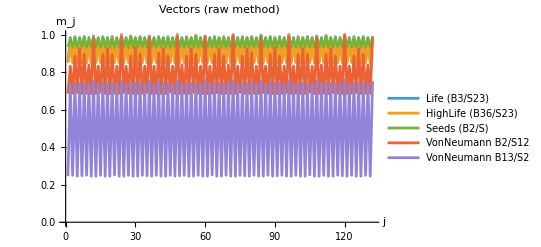

```mathematica
ListLinePlot[Values[vecsRaw],PlotLegends->Keys[vecsRaw],AxesLabel->{"j","m_j"},PlotLabel->"Vectors (raw method)",PlotRange->All]
```

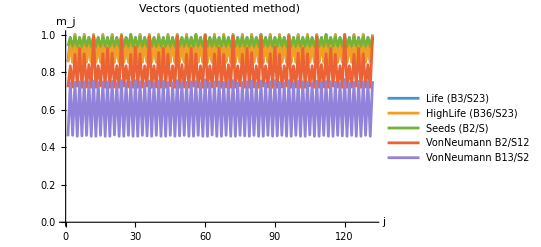

```mathematica
ListLinePlot[Values[vecsRot],PlotLegends->Keys[vecsRot],AxesLabel->{"j","m_j"},PlotLabel->"Vectors (quotiented method)",PlotRange->All]
```

```mathematica
MatrixPlot[distRaw,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameTicks->{{Table[{i,ruleKeys⟦i⟧},{i,5}],None},{Table[{i,ruleKeys⟦i⟧},{i,5}],None}},PlotLabel->"Cosine distance (raw)",ImageSize->450]
```

-Graphics-

```mathematica
MatrixPlot[distRot,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameTicks->{{Table[{i,ruleKeys⟦i⟧},{i,5}],None},{Table[{i,ruleKeys⟦i⟧},{i,5}],None}},PlotLabel->"Cosine distance (quotiented)",ImageSize->450]
```

-Graphics-

The 3 life-like rules (Moore neighborhood) cluster much closer to each other (cosine distance ~0.0001-0.0065) than to the 2 Von Neumann-neighborhood rules (~0.05-0.09) -- the change in neighborhood, not the specific B/S set, is what separates rules the most in this space. Both graph-construction methods (raw and translation-quotiented) agree closely for 4 of the 5 rules; the exception is VonNeumann B13/S2, which is also the only one with a notable fraction (~24%) of samples that did not resolve within 150 steps, suggesting long-period or chaotic dynamics for that rule -- consistent with the quotiented method (which merges translation-equivalent configurations) giving a more stable estimate there.

Life and Life+B8 (revive with 8 live neighbors) give an identical vector -- cosine distance 0 -- at this grid size: the rule of reviving when all neighbors are alive never fires in a way that changes the graph's cycle structure once quotiented. Life+S8 (stay alive with 8 neighbors) does produce a slightly different vector (distance 0.0005 from the other two), though the difference is small. This suggests that, at least at this space size, the survival modification has more structural impact than the birth modification.

## Functions

## Unprotected functions

```mathematica
Unprotect[RulePlot];

Quiet[RulePlot[CellularAutomaton[{0,1,0}],opts:OptionsPattern[]]=.];
Quiet[RulePlot[CellularAutomaton[{0,1,1/2}],opts:OptionsPattern[]]=.];

RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]]:=Module[{imgSize=Lookup[{opts},ImageSize,100],legend=Lookup[{opts},PlotLegends,None],restOpts=FilterRules[DeleteCases[{opts},(ImageSize|PlotLegends|ColorRules)->_],Options[Graphics]],ref,caseGfx,xCoords,xMin,xMax},ref=RulePlot[CellularAutomaton[{0,2,r}]];
caseGfx=ref[[1,1,1,-1]];
xCoords=Sort@Cases[ref[[1,2]],Line[{{x_,_},{x_,_}}]:>x,Infinity];
xMin=xCoords[[-2]];
xMax=Last[xCoords];
With[{g=Graphics[{caseGfx,{GrayLevel[0.8],{Line[{{xMin,0},{xMin,1}}],Line[{{xMax,0},{xMax,1}}]},{Line[{{xMin,0},{xMax,0}}],Line[{{xMin,1},{xMax,1}}]}}},ImageSize->imgSize,Sequence@@restOpts]},If[legend===None,g,Legended[g,legend]]]];

Protect[RulePlot];
```

SetDelayed::write: Tag RulePlot in RulePlot[CellularAutomaton[{0,1,r_}],opts:OptionsPattern[]] is Protected.

## Plot functions

```mathematica
colorRules[n_:10]:=Join[{0->RGBColor[1., 1., 1.]},Table[k->ColorData["Rainbow"][k/(n)],{k,1,(n)}]];
```

```mathematica
CaRulePlot[ca_Subscript,opts:OptionsPattern[]]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],opts,ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
rulialGraph[trans_,colorA_:Red,colorB_:Blue,labelA_:"Delete Last State",labelB_:"Minor inverse rule"]:=Module[
{
edges=Join[trans[[1]],trans[[2]]],
edgeStyles=Join[(#->Directive[colorA,Thick])&/@trans[[1]],(#->Directive[colorB,Thick])&/@trans[[2]]],
nodePlot=Function[v,If[v[[2]]<1,Graphics[{GrayLevel[0.9],Rectangle[]},ImageSize->{30,25}],RulePlot[CellularAutomaton[v],ImageSize->{Automatic,30},ColorRules->colorRules]]]
},
Legended[
LayeredGraph[
Graph[
edges,
EdgeStyle->edgeStyles,
VertexShapeFunction->(Inset[Column[{nodePlot[#2],Style[Subscript[#2[[1]],#2[[2]],1],Small,Black]},Alignment->Center],#1]&),
VertexSize->{0.11,100.03}
],
ImageSize->{Automatic,Automatic},
AspectRatio->2],
LineLegend[{colorA,colorB},{labelA,labelB}]
]
]
```

## Functions

```mathematica
getRules[s_,n_]:=ParallelMap[Subscript[#,s,n]&,Range[0,s^(s^n)-1]]
```

```mathematica
CaRulePlot[ca_Subscript,opts:OptionsPattern[]]:=
RulePlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2}],ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
CaArrayPlot[ca_Subscript,s_,t_,opts:OptionsPattern[]]:=
ArrayPlot[CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t],ColorRules->colorRules[ca[[2]]-1],opts];
```

```mathematica
CaArray[ca_Subscript,s_,t_]:=Module[{},
CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]
]
```

### Direct relations

```mathematica
addData[rulesIn_List,dataIn_Association:<||>]:=Module[
{
data=dataIn,rules=rulesIn,
inverseRules,mirrorRules,stateRules,neighborRules,joinRules
},
{inverseRules,mirrorRules,stateRules,neighborRules}=Parallelize[{
DeleteDuplicates@Flatten[Table[Map[rule->#&,InverseRules[rule]],{rule,rules}]],
DeleteDuplicates@Flatten[Table[Map[rule->#&,MirrorRules[rule]],{rule,rules}]],
Select[Map[#->DeleteState[#]&,rules],#[[2]]=!=Null&],
Select[Map[#->DeleteNeighbor[#]&,rules],#[[2]]=!=Null&]
}];

<|
"inverse"->DeleteDuplicates[Join[Lookup[dataIn,"inverse",{}],inverseRules]],
"mirror"->DeleteDuplicates[Join[Lookup[dataIn,"mirror",{}],mirrorRules]],
"state"->DeleteDuplicates[Join[Lookup[dataIn,"state",{}],stateRules]],
"neighbor"->DeleteDuplicates[Join[Lookup[dataIn,"neighbor",{}],neighborRules]]
|>
]
```

```mathematica
reduce[data_]:=Module[{dataUnq},
dataUnq=ReplaceAll[data,ParallelMap[Reverse,data["inverse"]]];
dataUnq=ReplaceAll[dataUnq,ParallelMap[Reverse,dataUnq["mirror"]]];
ParallelMap[DeleteDuplicates,dataUnq[[{"inverse","join","state","neighbor"}]]]
]
```

#### InverseRule

```mathematica
InverseRules[ca_Subscript]:=Module[
{
r=ca[[1]],s=ca[[2]],n=(ca[[3]]-1)/2,
L=ca[[2]]^ca[[3]],outputs,tuples,perms,res
},
outputs=Reverse[IntegerDigits[r,s,L]];(*outputs[[k]]=salida de la vecindad k-1*)
tuples=IntegerDigits[#,s,2n+1]&/@Range[0,L-1];(*tuples[[k]]=vecindad k-1 como n-tupla*)
perms=Permutations[Range[0,s-1]];(*solo s! permutaciones de ESTADOS*)
res=Sort@DeleteDuplicates@Table[
Module[
{pi=AssociationThread[Range[0,s-1]->perm],newOut=ConstantArray[0,L]},
Do[
newOut[[FromDigits[pi/@tuples[[k]],s]+1]]=pi[outputs[[k]]]
,{k,1,L}
];
FromDigits[Reverse[newOut],s]]
,{perm,perms}
];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Mirror Rules

```mathematica
MirrorRules[ca_Subscript]:=Module[{pos,rule,assoc,res},
pos=IntegerDigits[#,ca[[2]],ca[[3]]]&/@Range[0,ca[[2]]^ca[[3]]-1];
rule=IntegerDigits[ca[[1]],ca[[2]],Length[pos]];
assoc=Transpose[{pos,rule}];
res=Sort@DeleteDuplicates[{ca[[1]],FromDigits[
SortBy[{Reverse[#[[1]]],#[[2]]}&/@assoc,#[[1]]&][[;;,2]],
ca[[2]]
]}];
Subscript[#,ca[[2]],ca[[3]]]&/@res
]
```

#### Delete state

```mathematica
DeleteState[ca_Subscript]:=Module[{vector,pos,rule,newpos},If[ca[[2]]==1,Return[];];
vector=IntegerDigits[Range[ca[[2]]^ca[[3]]-1,0,-1],ca[[2]]];
pos=Position[vector,ca[[2]]-1][[;;,1]];
rule=IntegerDigits[ca[[1]],ca[[2]],ca[[2]]^ca[[3]]];
If[rule[[pos]]==ConstantArray[0,Length[pos]]&&Not@ContainsAny[rule,{ca[[2]]-1}],
(*Puede eliminarse ese estado*)
newpos=Complement[Range[ca[[2]]^ca[[3]],1,-1],pos];
Subscript[FromDigits[rule[[newpos]],ca[[2]]-1],ca[[2]]-1,ca[[3]]],
(*No puede eliminarse*)
Null]];
```

#### Delete neighbor

```mathematica
DeleteNeighbor[ca_Subscript]:=Module[
{r,s,n,rv,tuples,ruleIdx,indepQ,ip,relPos,nRed,redRV},
r=ca[[1]];s=ca[[2]];n=ca[[3]];
If[n==1,Return[];];
rv=IntegerDigits[r,s,s^n];
tuples=IntegerDigits[#,s,n]&/@Range[s^n-1,0,-1];
ruleIdx[inp_]:=s^n-FromDigits[inp,s];
indepQ[pos_]:=AllTrue[tuples,Function[inp,SameQ@@Table[rv[[ruleIdx[ReplacePart[inp,pos->v]]]],{v,0,s-1}]]];
ip=Select[Range[n],indepQ];
If[Length[ip]==0,Null,relPos=Complement[Range[n],{ip[[1]]}];(*solo elimina 1 posición*)nRed=n-1;
redRV=rv[[ruleIdx[ReplacePart[ConstantArray[0,n],Thread[relPos->#]]]]]&/@(IntegerDigits[#,s,nRed]&/@Range[s^nRed-1,0,-1]);
Subscript[FromDigits[redRV,s],s,n-1]]]
```

### Graph relations

```mathematica
MakeGraph[ca_Subscript,spaceSize_]:=Module[{inits},
inits=Tuples[Range[0,ca[[2]]-1],spaceSize];
Graph[
Map[
FromDigits[#[[1]],2]->FromDigits[#[[2]],2]&,(CaArray[ca,#,1]&/@inits)],
VertexLabels->Automatic]
]
```

```mathematica
EigenvaluesGraph[g_Graph]:=Eigenvalues[N[Normal[AdjacencyMatrix[g]]]]
```

```mathematica
EigenvaluesGraphDistance[g1_Graph,g2_Graph]:=Module[{ev1,ev2},
ev1=Eigenvalues[N[Normal[AdjacencyMatrix[g1]]]];
ev2=Eigenvalues[N[Normal[AdjacencyMatrix[g2]]]];
CosineDistance[ev1,ev2]
]
```